```mathematica
-(1+ⅈ Δ+ⅈ Abs[a]^2)a + s
%/.{a->q+ⅈ p, s->sq+ⅈ sp}
%//ComplexExpand//Simplify
%//ReIm//ComplexExpand//Simplify
```

s+a (-1-ⅈ Δ-ⅈ Abs[a]^2)

ⅈ sp+sq+(ⅈ p+q) (-1-ⅈ Δ-ⅈ Abs[ⅈ p+q]^2)

p^3-q+p q^2+sq+p Δ-ⅈ (p+p^2 q+q^3-sp+q Δ)

{p^3-q+sq+p (q^2+Δ),-p-p^2 q-q^3+sp-q Δ}

```mathematica
{-q - (Δ+q^2+p^2)p+sq,
-p+(Δ+q^2+p^2)q+sp}//ComplexExpand//Simplify
```

{-p^3-q+sq-p (q^2+Δ),-p+p^2 q+q^3+sp+q Δ}

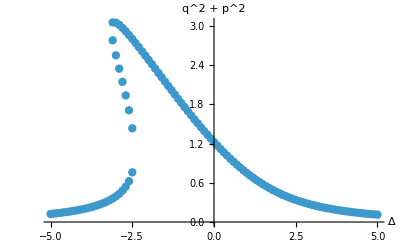

```mathematica
eq = {p^3-q+sq+p (q^2+Δ),
-p-p^2 q-q^3+sp-q Δ}/.{sp->0,sq->1.75};
tab=Table[
{Δ->det,NSolve[(eq/.{Δ->det})==0,{q,p},Reals]},
{det,-5,5,.1}
];
format[row_]:=Module[
{det,quads},
{det,quads}=row;
Flatten[{det,#}]&/@quads
]
tab2=format/@tab;
points=Thread[{Δ/.tab2//Flatten,q^2+p^2/.tab2//Flatten}];
ListPlot[points, AxesLabel->{"Δ","q^2 + p^2"}, PlotStyle->PointSize[0.015]]
```

{2-q-p (p^2+q^2+Δ),-p+q (p^2+q^2+Δ)}

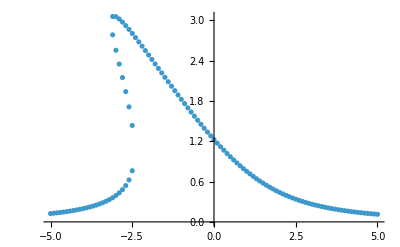

```mathematica
eq={-q - (Δ+q^2+p^2)p+sq,
-p+(Δ+q^2+p^2)q+sp}/.{sp->0,sq->1.75};
tab=Table[
{Δ->det,NSolve[(eq/.{Δ->det})==0,{q,p},Reals]},
{det,-5,5,0.1}
];
{2-q-p (p^2+q^2+Δ),-p+q (p^2+q^2+Δ)}

format[row_]:=Module[
{det,quads},
{det,quads}=row;
Flatten[{det,#}]&/@quads
]
tab2=format/@tab;

points=Thread[{Δ/.tab2//Flatten,q^2+p^2/.tab2//Flatten}];
ListPlot[points]
```